## EWS plot for Fussmann MODEL

## Import data

### EWS data

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/hopf_fussmann_2000"];
```

```mathematica
(* raw EWS data *)
ewsChlorRaw=Import["model/data_export/ews_stat_sweep_long/ews_chlor.csv"];
ewsBrachRaw=Import["model/data_export/ews_stat_sweep_long/ews_brach.csv"];
```

```mathematica
(* power spectrum data *)
pspecChlorRaw=Import["model/data_export/ews_stat_sweep_long/pspec_chlor.csv"];
pspecBrachRaw=Import["model/data_export/ews_stat_sweep_long/pspec_brach.csv"];
```

### Bifurcation data

```mathematica
bifPtsChlor=Import["data/bifPtsChlor.mat"];
bifPtsBrach=Import["data/bifPtsBrach.mat"];
```

```mathematica
(* clear out points that go beyond max dilution rate on plot *)
bifPtsChlor=Table[DeleteCases[bifPtsChlor[[i]],{x_,_}/;x>1.5],{i,1,Length[bifPtsChlor]}];
bifPtsBrach=Table[DeleteCases[bifPtsBrach[[i]],{x_,_}/;x>1.5],{i,1,Length[bifPtsBrach]}];
```

```mathematica
(* bifurcation points (from XPPAUT) *)
bif1=0.009;
bif2=0.151;
bif3=0.970;
bif4=1.427;
```

### General figure parameters

```mathematica
imgs=700;
aratio=0.18;
padding={{60,60},{20,20}};
{{padLeft,padRight},{padBottom,padTop}}=padding;
lt=0.006;
colChlor=Darker[TMBcolours[[1]],0.15];
colBrach=Darker[TMBcolours[[4]],0.15];
{colChlor,colBrach}
labelPos=Scaled[{0.04,0.85}];
```

{RGBColor[0.31315445, 0.43076214999999995, 0.6033283],RGBColor[0.7841471, 0.3277821, 0.17780215]}

```mathematica
deltaVals=Union[ewsChlorRaw[[2;;,1]]];
dMax =1.5;
```

```mathematica
ewsChlorRaw[[1]]
```

{Delta,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Lag-6 AC,Coefficient of variation,Skewness,Kurtosis,AIC fold,AIC hopf,AIC null,Coherence factor,Params fold,Params hopf,Params null,Smax}

## Bifurcation diagram

```mathematica
(* chlorella bifurcation plot *)
bifPlotChlor=ListLinePlot[bifPtsChlor,
PlotStyle->Table[{colChlor,Thickness[lt]},{i,1,Length[bifPtsChlor]}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,dMax},{-4.2/40,4.2}*1000000},
Frame->{{True,False},{True,True}},
FrameLabel->{{"Chlor. (10^6 cells/ml)",Style["Brach. (females/ml)",White]},{"",""}},
FrameTicks->{{Transpose[{Range[-4/40,4]*1000000,Range[0,4]}],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->0.28,
PlotRangeClipping->False,
ImagePadding->padding,
Epilog->{Directive[{Black}],
Directive[{Black}],Text[Style["a",14,Bold],Scaled[{0.04,0.9}]]}];
```

```mathematica
(* brachionus bif *)
bifPlotBrach=ListLinePlot[bifPtsBrach,
PlotRange->{{0,dMax},{-59/40,59}},
PlotStyle->Table[{colBrach,Thickness[lt]},{i,1,Length[bifPtsBrach]}],
LabelStyle->14,
InterpolationOrder->1,
Frame->{{False,True},{True,True}},
FrameLabel->{{Style["Chlor. (10^6 cells/ml)",White],"Brach. (females/ml)"},{"",""}},
FrameTicks->{{None,Range[0,60,10]},{None,None}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->0.28,
PlotRangeClipping->False,
ImagePadding->padding];
```

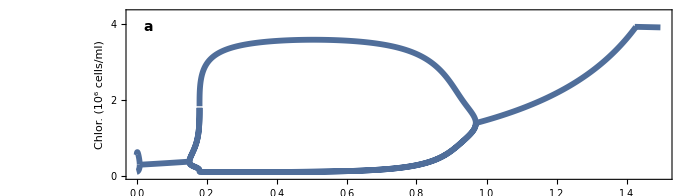
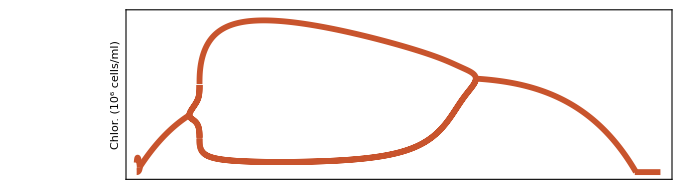

```mathematica
(* put together *)
bifPlot=Overlay[{bifPlotChlor,bifPlotBrach}]
```

## Plots of EWS against delta

```mathematica
ewsChlorRaw[[1]]
```

{Delta,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Lag-6 AC,Coefficient of variation,Skewness,Kurtosis,AIC fold,AIC hopf,AIC null,Coherence factor,Params fold,Params hopf,Params null,Smax}

### Variance

```mathematica
index=Position[ewsChlorRaw[[1]],"Variance"][[1,1]];
```

```mathematica
varChlor=ewsChlorRaw[[2;;,index]];
varBrach=ewsBrachRaw[[2;;,index]];
```

```mathematica
deltaVals//Dimensions
```

{320}

```mathematica
varChlor//Dimensions
```

{320}

```mathematica
varPlotChlor=ListLogPlot[Transpose[{deltaVals,varChlor}],
LabelStyle->14,
Joined->True,
PlotRange->{{0,dMax},{10^(-6.5),1000}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"Var",""},{"",""}},
FrameTicks->{{{{10^(-6),"10^-6"},{10^(-4),"10^-4"},{10^(-2),"10^-2"},{1,1},{100,100}},None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["b",14,Bold],labelPos]}
];
```

```mathematica
varPlotBrach=ListLogPlot[Transpose[{deltaVals,varBrach}],
LabelStyle->14,
Joined->True,
PlotRange->{{0,dMax},{10^(-6.5),1000}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Var"},{"",""}},
FrameTicks->{{None,{{10^(-6),"10^-6"},{10^(-4),"10^-4"},{10^(-2),"10^-2"},{1,1},{100,100}}},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

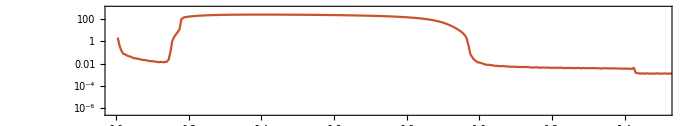
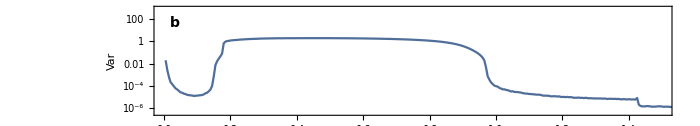

```mathematica
varPlot=Overlay[{varPlotBrach,varPlotChlor}]
```

### Coefficient of variation

```mathematica
index=Position[ewsChlorRaw[[1]],"Coefficient of variation"][[1,1]];
```

```mathematica
cvarChlor=ewsChlorRaw[[2;;,index]];
cvarBrach=ewsBrachRaw[[2;;,index]];
```

```mathematica
cvarPlotChlor=ListLogPlot[Transpose[{deltaVals,cvarChlor}],
LabelStyle->14,
Joined->True,
PlotRange->{{0,dMax},All},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"C.V.",""},{"",""}},
FrameTicks->{{{{10^(-3),"10^-3"},{10^(-2),"10^-2"},{10^(-1),"10^-1"},{1,1},{10,10}},None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["c",14,Bold],labelPos]}];
```

```mathematica
cvarPlotBrach=ListLogPlot[Transpose[{deltaVals,cvarBrach}],
LabelStyle->14,
Joined->True,
PlotRange->{{0,dMax},All},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","C.V."},{"",""}},
FrameTicks->{{None,{{10^(-3),"10^-3"},{10^(-2),"10^-2"},{10^(-1),"10^-1"},{1,1},{10,10}}},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

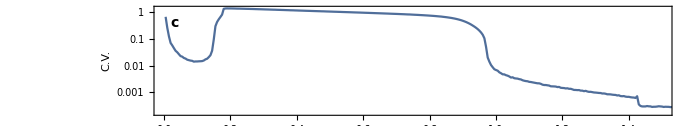
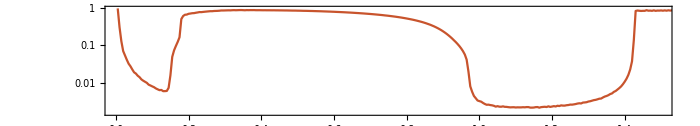

```mathematica
cvarPlot=Overlay[{cvarPlotChlor,cvarPlotBrach}]
```

### Lag-1 AC

```mathematica
index=Position[ewsChlorRaw[[1]],"Lag-1 AC"][[1,1]];
```

```mathematica
acChlor=ewsChlorRaw[[2;;,index]];
acBrach=ewsBrachRaw[[2;;,index]];
```

```mathematica
acPlotChlor=ListLinePlot[Transpose[{deltaVals,acChlor}],
LabelStyle->14,
PlotRange->{{0,dMax},{-0.2,1}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"Lag-1 AC",""},{"",""}},
FrameTicks->{{Range[-1,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["d",14,Bold],labelPos]}];
```

```mathematica
acPlotBrach=ListLinePlot[Transpose[{deltaVals,acBrach}],
LabelStyle->14,
PlotRange->{{0,dMax},{-0.2,1}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Lag-1 AC"},{"",""}},
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

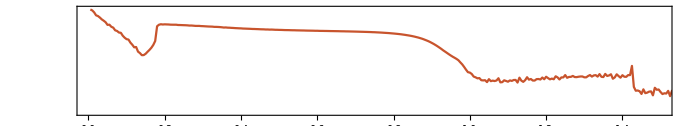
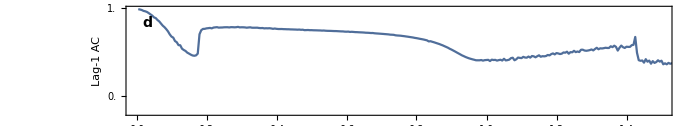

```mathematica
acPlot=Overlay[{acPlotBrach,acPlotChlor}]
```

### Lag-2 AC

```mathematica
index=Position[ewsChlorRaw[[1]],"Lag-2 AC"][[1,1]];
```

```mathematica
acChlor=ewsChlorRaw[[2;;,index]];
acBrach=ewsBrachRaw[[2;;,index]];
```

```mathematica
acPlotChlor=ListLinePlot[Transpose[{deltaVals,acChlor}],
LabelStyle->14,
PlotRange->{{0,dMax},{-1,1}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"Lag-2 AC",""},{"",""}},
FrameTicks->{{Range[-1,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["d",14,Bold],labelPos]}];
```

```mathematica
acPlotBrach=ListLinePlot[Transpose[{deltaVals,acBrach}],
LabelStyle->14,
PlotRange->{{0,dMax},{-1,1}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Lag-2 AC"},{"",""}},
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

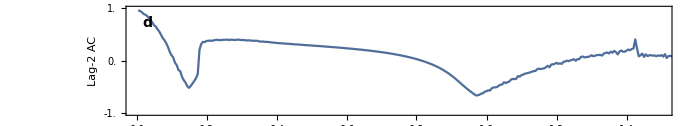
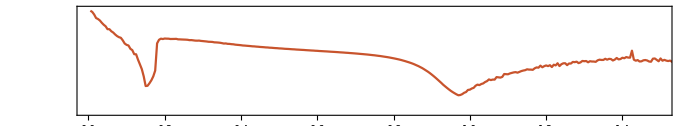

```mathematica
ac2Plot=Overlay[{acPlotChlor,acPlotBrach}]
```

### Lag-3 AC

```mathematica
index=Position[ewsChlorRaw[[1]],"Lag-3 AC"][[1,1]];
```

```mathematica
acChlor=ewsChlorRaw[[2;;,index]];
acBrach=ewsBrachRaw[[2;;,index]];
```

```mathematica
acPlotChlor=ListLinePlot[Transpose[{deltaVals,acChlor}],
LabelStyle->14,
PlotRange->{{0,dMax},{-1,1}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"Lag-3 AC",""},{"",""}},
FrameTicks->{{Range[-1,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["c",14,Bold],labelPos]}];
```

```mathematica
acPlotBrach=ListLinePlot[Transpose[{deltaVals,acBrach}],
LabelStyle->14,
PlotRange->{{0,dMax},{-1,1}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Lag-3 AC"},{"",""}},
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

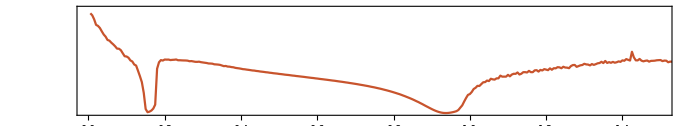
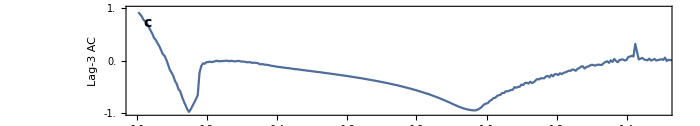

```mathematica
ac3Plot=Overlay[{acPlotBrach,acPlotChlor}]
```

### Lag-6 AC

```mathematica
index=Position[ewsChlorRaw[[1]],"Lag-6 AC"][[1,1]];
```

```mathematica
acChlor=ewsChlorRaw[[2;;,index]];
acBrach=ewsBrachRaw[[2;;,index]];
```

```mathematica
acPlotChlor=ListLinePlot[Transpose[{deltaVals,acChlor}],
LabelStyle->14,
PlotRange->{{0,dMax},{-1,1}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"Lag-6 AC",""},{"",""}},
FrameTicks->{{Range[-1,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["d",14,Bold],labelPos]}];
```

```mathematica
acPlotBrach=ListLinePlot[Transpose[{deltaVals,acBrach}],
LabelStyle->14,
PlotRange->{{0,dMax},{-1,1}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Lag-6 AC"},{"",""}},
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

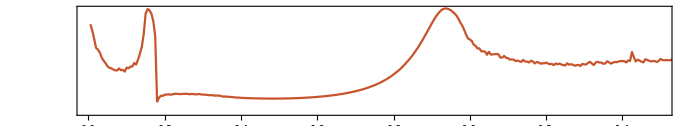
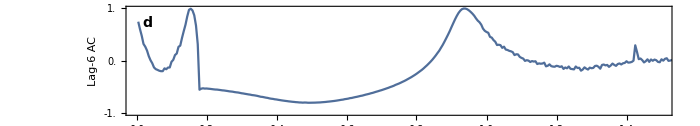

```mathematica
ac6Plot=Overlay[{acPlotBrach,acPlotChlor}]
```

### Smax

```mathematica
index=Position[ewsChlorRaw[[1]],"Smax"][[1,1]];
```

```mathematica
smaxChlor=ewsChlorRaw[[2;;,index]];
smaxBrach=ewsBrachRaw[[2;;,index]];
```

```mathematica
smaxPlotChlor=ListLogPlot[Transpose[{deltaVals,smaxChlor}],
LabelStyle->14,
Joined->True,
PlotRange->{{0,dMax},{10^(-7.5),500}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"S_max",""},{"",""}},
FrameTicks->{{{{10^(-6),"10^-6"},{10^(-4),"10^-4"},{10^(-2),"10^-2"},{1,"1"},{100,100}},None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["e",14,Bold],labelPos]}];
```

```mathematica
smaxPlotBrach=ListLogPlot[Transpose[{deltaVals,smaxBrach}],
LabelStyle->14,
Joined->True,
PlotRange->{{0,dMax},{10^(-7.5),500}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","S_max"},{"",""}},
FrameTicks->{{None,{{10^(-6),"10^-6"},{10^(-4),"10^-4"},{10^(-2),"10^-2"},{1,1},{100,100}}},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

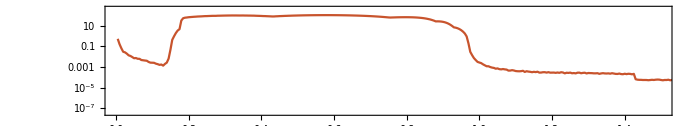
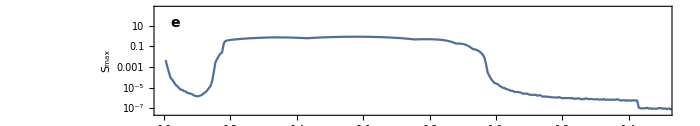

```mathematica
smaxPlot=Overlay[{smaxPlotBrach,smaxPlotChlor}]
```

### Coherence Factor

```mathematica
index=Position[ewsChlorRaw[[1]],"Coherence factor"][[1,1]];
```

```mathematica
cfChlor=ewsChlorRaw[[2;;,index]];
cfBrach=ewsBrachRaw[[2;;,index]];
```

```mathematica
cfPlotChlor=ListLogPlot[Transpose[{deltaVals,cfChlor}],
LabelStyle->14,
Joined->True,
PlotRange->{{0,dMax},{10^(-7.5),10}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"Coherence",""},{"",""}},
FrameTicks->{{{{10^(-6),"10^-6"},{10^(-4),"10^-4"},{10^(-2),"10^-2"},{1,"1"}},None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["e",14,Bold],labelPos]}];
```

```mathematica
cfPlotBrach=ListLogPlot[Transpose[{deltaVals,cfBrach}],
LabelStyle->14,
Joined->True,
PlotRange->{{0,dMax},All},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Coherence"},{"",""}},
FrameTicks->{{None,{{10^(-4),"10^-4"},{10^(-2),"10^-2"},{1,1},{100,100}}},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

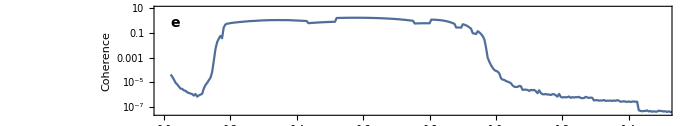
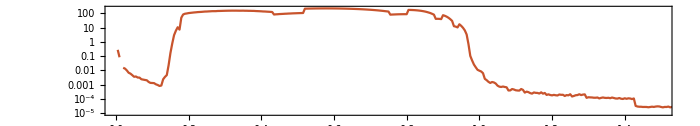

```mathematica
cfPlot=Overlay[{cfPlotChlor,cfPlotBrach}]
```

### AIC weight fold

```mathematica
index=Position[ewsChlorRaw[[1]],"AIC fold"][[1,1]];
```

```mathematica
aicfoldChlor=ewsChlorRaw[[2;;,index]];
aicfoldBrach=ewsBrachRaw[[2;;,index]];
```

```mathematica
aicfoldPlotChlor=ListLinePlot[Transpose[{deltaVals,aicfoldChlor}],
LabelStyle->14,
PlotRange->{{0,dMax},{-0.1,1.1}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"w_fold(C)",""},{"",""}},
FrameTicks->{{Range[0,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

```mathematica
aicfoldPlotBrach=ListLinePlot[Transpose[{deltaVals,aicfoldBrach}],
LabelStyle->14,
PlotRange->{{0,dMax},{-0.1,1.1}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","w_fold(B)"},{"",""}},
FrameTicks->{{None,Range[0,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

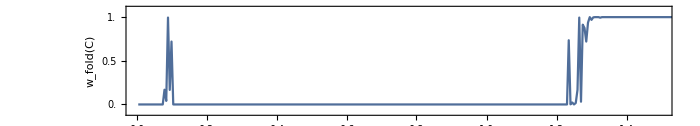
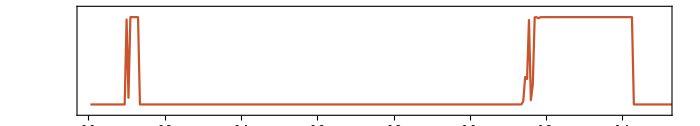

```mathematica
aicfoldPlot=Overlay[{aicfoldPlotChlor,aicfoldPlotBrach}]
```

### AIC weight hopf

```mathematica
index=Position[ewsChlorRaw[[1]],"AIC hopf"][[1,1]];
```

```mathematica
aichopfChlor=ewsChlorRaw[[2;;,index]];
aichopfBrach=ewsBrachRaw[[2;;,index]];
```

```mathematica
aichopfPlotChlor=ListLinePlot[Transpose[{deltaVals,aichopfChlor}],
LabelStyle->14,
PlotRange->{{0,dMax},{-0.1,1.3}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"w_hopf",""},{"Dilution rate δ (per day)",""}},
FrameTicks->{{Range[0,1,0.5],Automatic},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->{{padLeft,padRight},{padBottom*1.3,padTop}},
Epilog->{Directive[{Black}],Text[Style["f",14,Bold],labelPos]}];
```

```mathematica
aichopfPlotBrach=ListLinePlot[Transpose[{deltaVals,aichopfBrach}],
LabelStyle->14,
PlotRange->{{0,dMax},{-0.1,1.3}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","w_hopf"},{"Dilution rate δ (per day)",""}},
FrameTicks->{{None,Range[0,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->{{padLeft,padRight},{padBottom*2.2,padTop}}];
```

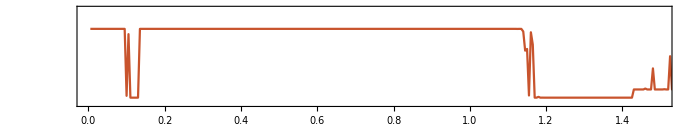
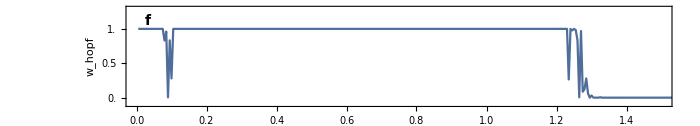

```mathematica
aichopfPlot=Overlay[{aichopfPlotBrach,aichopfPlotChlor}]
```

### AIC weight Null

```mathematica
index=Position[ewsChlorRaw[[1]],"AIC null"][[1,1]];
```

```mathematica
aicNullChlor=ewsChlorRaw[[2;;,index]];
aicNullBrach=ewsBrachRaw[[2;;,index]];
```

```mathematica
aicNullPlotChlor=ListLinePlot[Transpose[{deltaVals,aicNullChlor}],
LabelStyle->14,
PlotRange->{{0,dMax},{-0.1,1.2}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"w_null(C)",""},{"Dilution rate δ (per day)",""}},
FrameTicks->{{Range[0,1,0.5],Automatic},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->{{padLeft,padRight},{padBottom*1.3,padTop}},
Epilog->{Directive[{Black}],Text[Style["f",14,Bold],labelPos]}];
```

```mathematica
aicNullPlotBrach=ListLinePlot[Transpose[{deltaVals,aicNullBrach}],
LabelStyle->14,
PlotRange->{{0,dMax},{-0.1,1.2}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","w_null(B)"},{"Dilution rate δ (per day)",""}},
FrameTicks->{{None,Range[0,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->{{padLeft,padRight},{padBottom*2.2,padTop}}];
```

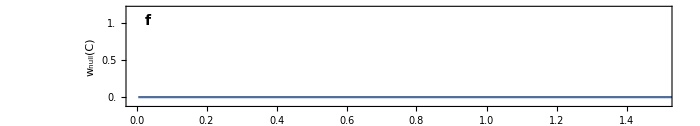
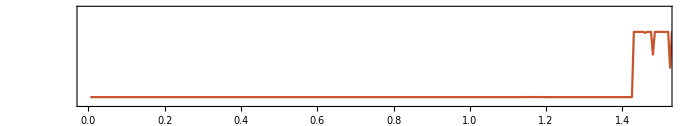

```mathematica
aicNullPlot=Overlay[{aicNullPlotChlor,aicNullPlotBrach}]
```

## Power spectrum heat map against delta

Plot the power spectrum against delta

```mathematica
pspecChlorRaw//Dimensions
```

{13120,3}

```mathematica
specPlotChlor=ListDensityPlot[pspecChlorRaw,
LabelStyle->14,
(*PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["S(ω)",12]],Position[{0.1,0.1}]]*)
ScalingFunctions->{None,None,"Log"},
InterpolationOrder->0,
AspectRatio->aratio,
ImageSize->imgs,
Frame->{{True,True},{True,True}},
FrameLabel->{{"ω",""},{"Dilution rate δ (per day)",""}},
FrameTicks->{{All,Automatic},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,FontOpacity->0}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->{{padLeft,padRight},{padBottom*2.2,padTop}}];
```

```mathematica
specPlotBrach=ListDensityPlot[pspecBrachRaw,
LabelStyle->14,
(*PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["S(ω)",12]],Position[{0.1,0.1}]]*)
ScalingFunctions->{None,None,"Log"},
InterpolationOrder->0,
AspectRatio->aratio,
ImageSize->imgs,
Frame->{{True,True},{True,True}},
FrameLabel->{{"ω",""},{"Dilution rate δ (per day)",""}},
FrameTicks->{{All,Automatic},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,FontOpacity->0}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->{{padLeft,padRight},{padBottom*2.2,padTop}}];
```

```mathematica
Grid[{{bifPlot},{specPlotChlor},{specPlotBrach}}];
```

## Grid all plots together

```mathematica
plotTemp=Grid[{{bifPlot},{varPlot},{ac3Plot},{ac6Plot},{smaxPlot},{aichopfPlot}},Spacings->{0,-1.5}];
```

```mathematica
(* Add vertical lines where bifurcations are *)
lHeight1=0.08;
lHeight2=3.02;
l1=Line[{{bif1,lHeight1},{bif1,lHeight2}}];
l2=Line[{{bif2,lHeight1},{bif2,lHeight2}}];
l3=Line[{{bif3,lHeight1},{bif3,lHeight2}}];
l4=Line[{{bif4,lHeight1},{bif4,lHeight2}}];
```

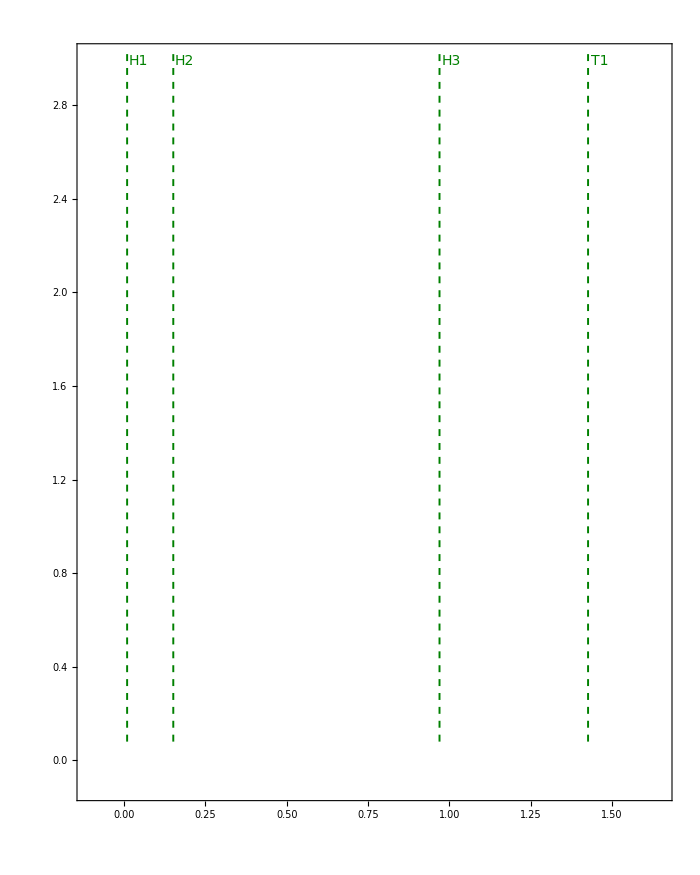
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics--Graphics-

```mathematica
ewsModelPlot=Overlay[{plotTemp,
Graphics[{{Darker[Green,0.5],Dashed,Thickness[0.002],l1},
{Darker[Green,0.5],Dashed,Thickness[0.002],l2},
{Darker[Green,0.5],Dashed,Thickness[0.002],l3},
{Darker[Green,0.5],Dashed,Thickness[0.002],l4},
{Text[Style["H1",14,Darker[Green,0.5]],{bif1+0.035,2.99}]},
{Text[Style["H2",14,Darker[Green,0.5]],{bif2+0.035,2.99}]},
{Text[Style["H3",14,Darker[Green,0.5]],{bif3+0.035,2.99}]},
{Text[Style["T1",14,Darker[Green,0.5]],{bif4+0.035,2.99}]}},
ImageSize->700,AspectRatio->1.25,Frame->True,
FrameStyle->Directive[Opacity[0]],
PlotRange->{{-0.11,1.65},{-0.11,3}}]
}
]
```

```mathematica
Export["figures/ews_model.png",ewsModelPlot,ImageResolution->200];
```

## Zoom in on T1

### Variance

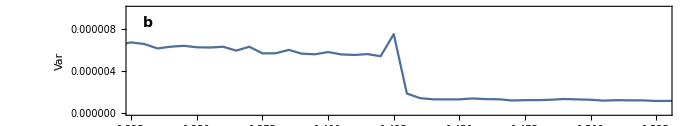

```mathematica
varPlotChlor=ListPlot[Transpose[{deltaVals,varChlor}],
LabelStyle->14,
Joined->True,
PlotRange->{{bif4-0.1,bif4+0.1},{0,0.00001}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"Var",""},{"",""}},
(*FrameTicks->{{{{10^(-6),"10^-6"},{10^(-4),"10^-4"},{10^(-2),"10^-2"},{1,1},{100,100}},None},{Automatic,Automatic}}*)
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["b",14,Bold],labelPos]}
]
```

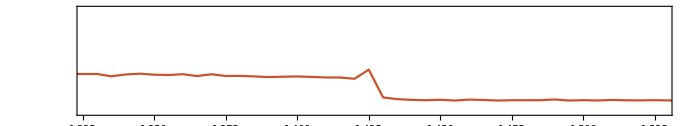

```mathematica
varPlotBrach=ListPlot[Transpose[{deltaVals,varBrach}],
LabelStyle->14,
Joined->True,
PlotRange->{{bif4-0.1,bif4+0.1},{0,0.01}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Var"},{"",""}},
FrameTicks->{{None,Automatic},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding]
```

```mathematica
varPlotT1=Overlay[{varPlotBrach,varPlotChlor}]
```

-Graphics--Graphics-

## Zoom in on H2

```mathematica
bif2
```

0.151

```mathematica
dmin=0.05;
dmax=0.16;
indexPos1=Scaled[{0.03,1.1}];
indexPos2=Scaled[{0.97,1.1}];
aratio=0.2;
imgs=500;
```

### Bifurcation diagram

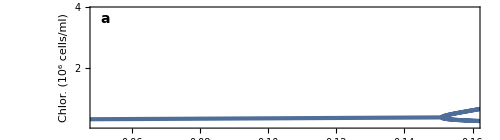
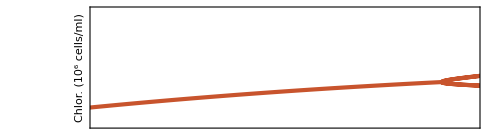

```mathematica
bifPlotH2=Overlay[{
Show[bifPlotChlor,PlotRange->{{dmin,dmax},All},PlotRangeClipping->True,ImageSize->imgs],
Show[bifPlotBrach,PlotRange->{{dmin,dmax},All},PlotRangeClipping->True,ImageSize->imgs]}
]
```

### Variance

```mathematica
varPlotChlor=ListPlot[Cases[Transpose[{deltaVals,varChlor}],{x_,_}/;dmin<=x<=dmax],
LabelStyle->14,
Joined->True,
PlotRangeClipping->False,
PlotRange->{{0.05,0.16},{0,0.0002}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"Var",""},{"",""}},
FrameTicks->{{Transpose[{10^(-4)*Range[0,2,1],Range[0,2,1]}],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["b",14,Bold],labelPos],
Directive[{colChlor}],Text[Style["×10^-4",14],indexPos1]}
];
```

```mathematica
varPlotBrach=ListPlot[Cases[Transpose[{deltaVals,varBrach}],{x_,_}/;dmin≤x≤dmax],
LabelStyle->14,
Joined->True,
PlotRangeClipping->False,
PlotRange->{{0.05,0.16},{0,0.1}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Var"},{"",""}},
FrameTicks->{{None,Transpose[{10^(-2)*Range[0,8,2],Range[0,8,2]}]},{None,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{colBrach}],Text[Style["×10^-2",14],indexPos2]}];
```

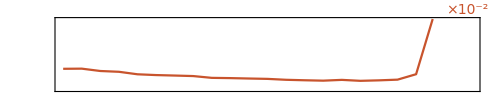
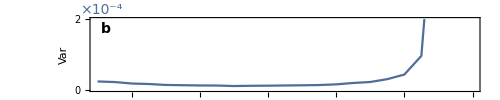

```mathematica
varPlotH2=Overlay[{varPlotBrach,varPlotChlor}]
```

### Smax

```mathematica
smaxPlotChlor=ListPlot[Cases[Transpose[{deltaVals,smaxChlor}],{x_,_}/;dmin<=x<=dmax],
LabelStyle->14,
Joined->True,
PlotRangeClipping->False,
PlotRange->{{0.05,0.16},{0,0.0001}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"S_max",""},{"",""}},
FrameTicks->{{Transpose[{10^(-4)*Range[0,2,1],Range[0,2,1]}],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["c",14,Bold],labelPos],
Directive[{colChlor}],Text[Style["×10^-4",14],indexPos1]}
];
```

```mathematica
smaxPlotBrach=ListPlot[Cases[Transpose[{deltaVals,smaxBrach}],{x_,_}/;dmin≤x≤dmax],
LabelStyle->14,
Joined->True,
PlotRangeClipping->False,
PlotRange->{{0.05,0.16},{0,0.03}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","S_max"},{"",""}},
FrameTicks->{{None,Transpose[{10^(-2)*Range[0,8,2],Range[0,8,2]}]},{None,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{colBrach}],Text[Style["×10^-2",14],indexPos2]}];
```

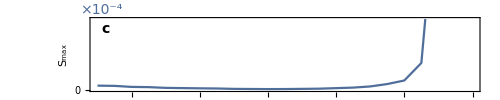
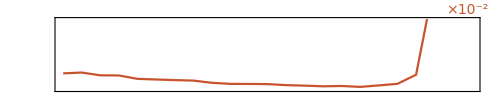

```mathematica
smaxPlotH2=Overlay[{smaxPlotChlor,smaxPlotBrach}]
```

### AIC weight hopf

```mathematica
aichopfPlotChlor=ListLinePlot[Transpose[{deltaVals,aichopfChlor}],
LabelStyle->14,
PlotRange->{{bif2-0.1,bif2+0.01},{-0.05,1.05}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"w_hopf",""},{"Dilution rate δ (per day)",""}},
FrameTicks->{{Range[0,1,0.5],Automatic},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->{{padLeft,padRight},{padBottom*1.3,padTop}},
Epilog->{Directive[{Black}],Text[Style["d",14,Bold],labelPos]}];
```

```mathematica
aichopfPlotBrach=ListLinePlot[Transpose[{deltaVals,aichopfBrach}],
LabelStyle->14,
PlotRange->{{bif2-0.1,bif2+0.01},{-0.05,1.05}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","w_hopf"},{"Dilution rate δ (per day)",""}},
FrameTicks->{{None,Range[0,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->{{padLeft,padRight},{padBottom*2.2,padTop}}];
```

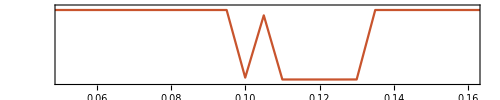
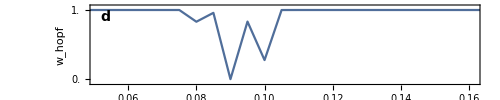

```mathematica
aichopfPlotH2=Overlay[{aichopfPlotBrach,aichopfPlotChlor}]
```

### Grid together

```mathematica
plotTemp=Grid[{{bifPlotH2},{varPlotH2},{smaxPlotH2},{aichopfPlotH2}},Spacings->{0,-0.5}]
```

-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-

```mathematica
(* Add vertical lines where bifurcations are *)
lHeight1=0.08;
lHeight2=3.2;
l1=Line[{{0.83,lHeight1},{0.83,lHeight2}}];
```

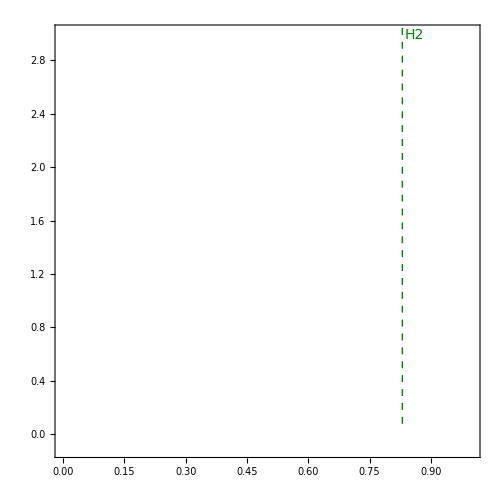
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics--Graphics-

```mathematica
ewsModelPlotH2=Overlay[{plotTemp,
Graphics[{{Darker[Green,0.5],Dashed,Thickness[0.002],l1},
{Text[Style["H2",14,Darker[Green,0.5]],{0.86,2.99}]}},
ImageSize->500,AspectRatio->1,Frame->True,
FrameStyle->Directive[Opacity[0]],
PlotRange->{{0,1},{-0.11,3}}]
}
]
```

```mathematica
Export["figures/ews_modelH2.png",ewsModelPlotH2,ImageResolution->200];
```

figures/ews_modelH2.png